# NLIT (Not-LIT) 9/9/21

[σ_tot]=μb=10^-4 fm^2
[σ_tot]=mb=10^-1 fm^2
[Lab photon energy] = MeV

dipole calculation from B. Gibson & D.R. Lehmann, PRC 13,2 (1976) (T=3/2 only!)
and Golak et al.

/home/kirscher/kette_repo/IRS/src_mathematica

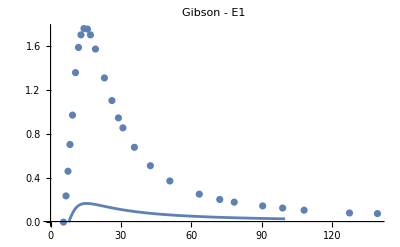

```mathematica
SetDirectory[NotebookDirectory[]]
He3DatamBarnGolak=Import["../data/he3_photo_diss_sigma_golak.dat","Data"];
He3DatamBarnGibson=Import["../data/he3_photo_diss_sigma_gibson.dat","Data"];Bhe=7.67;
hbarc=197.32858;
He3DataFm2=Transpose[{Transpose[He3DatamBarnGolak][[1]],Transpose[He3DatamBarnGolak][[2]] 10.^(-0)}];

σBethe[ω_,E0_,mM_]:=4 (8 Pi)/3 1./137. 1./(mM E0) (ω/E0-1)^(3./2.)/(ω/E0)^3;
Show[
ListPlot[He3DataFm2,PlotLabel->Style["Gibson - E1",Orange,22]],
Plot[hbarc^2 σBethe[ν,Bhe,938.],{ν,0,100},PlotRange->Full,AxesLabel->{"E_(photon, lab) [MeV]","σ_total^(diss . helion) [fm^2]"}]]
```

#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
ResourceFunction["MaTeXInstall"][]
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy,LinearSolve::luc]
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts}"}];

readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];
```

PacletObject[…]

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={1.5};
J0=0.5;
mIns=Range[-#,#,1]&/@Subscript[I, n];
lege="J_lit="<>ToString[#]&/@Subscript[I, n];
thresholdLIT=(10.)^(-6);
dH=1; (* this takes only every dH basis vector into account; ECCE: not benchmarked *)
```

```mathematica
ImgSize=900;
mnucl=938.3;
hbarsqO2m=hbarc^2/(2 mnucl);
αfine=1./137.;
hat[l_]:=Sqrt[2 l+1];

resultsDir=$HomeDirectory<>"/scratch/compton_tmp/out_3he/latestresults";

files=FileNames[All,resultsDir];
anzBas=Length[Select[files,StringMatchQ[#,"*mat*BasNR*"]&]]/Length[Subscript[I, n]];

SetDirectory[resultsDir];
dt=ToString[Import["dtype.dat"][[1]][[1]]];
datatype="Real64";
Which[dt=="float32",datatype="Real32",dt=="float64",datatype="Real64"];
Print["Read FORTRAN results from \n",Style[resultsDir,18,Red],"\nin\n",Style[dt,18,Red],"=",Style[datatype,18,Red],"\nformat for\nN_bases=",Style[anzBas,18,Red],"\nevolved bases for the expansion of the final state."];
```

Read FORTRAN results from 
/home/kirscher/scratch/compton_tmp/out_3he/latestresults
in
float64=Real64
format for
N_bases=1
evolved bases for the expansion of the final state.

#### Orthonormalization of the basis

the function matSqrts obtains transformation matrices to a basis whose elements correspond to the
1) orthogonal Eigenvectors of the original Norm matrix
2) barring those EVs whose Eigenvalues are smaller than the chosen threshold

```mathematica
Clear[normreg,matSqrts];

matSqrts[norm_,cutoff_:0]:=Block[{μ,transf,evs,ovsqi,ovsq,n},

{μ,transf}=Transpose[Select[Sort[Transpose[Eigensystem[norm]],#1[[1]]<#2[[1]]&],#[[1]]>cutoff&]];
evs=Eigenvalues[norm];
Print["min/max: ",MinMax[evs]];
n=Length[Select[evs,#<cutoff&]];
Print["(min/max) discarded elements: ",n," ",MinMax[Select[evs,#<cutoff&]]];
Print["elements < 0: ",Length[Select[evs,#<0.&]]];

ovsq=DiagonalMatrix[If[#<cutoff,0,Sqrt[#]]&/@evs];ovsqi=DiagonalMatrix[If[#<cutoff,0,1/Sqrt[#]]&/@evs];
(*{Drop[ovsq.es[[2]],-n],Transpose[Drop[ovsqi.es[[2]],-n]]}*)

trafma=(Transpose[transf].DiagonalMatrix[μ^(1/2)]);
invtrafma=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);
evm=(Transpose[invtrafma].norm).invtrafma;
evm=(evm+Transpose[evm])/2;(* symmetrize for stability *)
evv=Eigenvalues[evm];
Print["MinMax[Re] = ",MinMax[Re[evv]]];
Print["MinMax[Im] = ",MinMax[Im[evv]]];
(*Print[ArrayRules[SparseArray[evm]]];*)

{trafma,invtrafma}];

normreg[threshold_,norm_]:=Block[{es=Eigensystem[norm],μ,transf},{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];(Transpose[transf].DiagonalMatrix[μ^(-1/2)])];
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the initial state, i.e., J^π=(1/2)^+ for the helion

```mathematica
He3NormHamMat=readREAL8list["./mat_npp0.5^+"];
tmp=He3NormHamMat[[Range[1,Length[He3NormHamMat],2]]];
ActiveBasVHe3=ReadList["./Ssigbasv3heLIT_npp0.5^+.dat"];

BareDims=Table[ReadList["./BareBasDims_"<>ToString[nn]<>".dat"],{nn,Range[anzBas]}]
(*He3NormHamMat=tmp;*)
He3BasisDim=IntegerPart[Sqrt[Length[He3NormHamMat] 0.5]];
Print["N_(helion - full) = ",He3BasisDim];
Print["N_(helion - active) = ",Length[ActiveBasVHe3]];
He3Norm=ArrayReshape[He3NormHamMat[[1;;He3BasisDim^2]],{He3BasisDim,He3BasisDim}][[;;;;dH,;;;;dH]];
He3Ham=ArrayReshape[He3NormHamMat[[He3BasisDim^2+1;;]],{He3BasisDim,He3BasisDim}][[;;;;dH,;;;;dH]];
MinMax[Eigenvalues[He3Norm]]
```

{{93,68}}

N_(helion - full) = 93

N_(helion - active) = 93

{0.000107974,10.7505}

#### The initial state (helion ground state ^3 He ) -- in Norm-Eigen-Vector Basis

other parts of this section yield analytic information on the initial state

```mathematica
{He3Nmh,He3Nmhi}=matSqrts[He3Norm,thresholdLIT];
```

min/max: {0.000107974,10.7505}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

B(^3He) = -5.77468

Dim_full^helion = 93=^!93   ;     Dim_(non - singular)^helion = 93

Lowest EV's:{-5.77468,0.391301}

Norm=1.

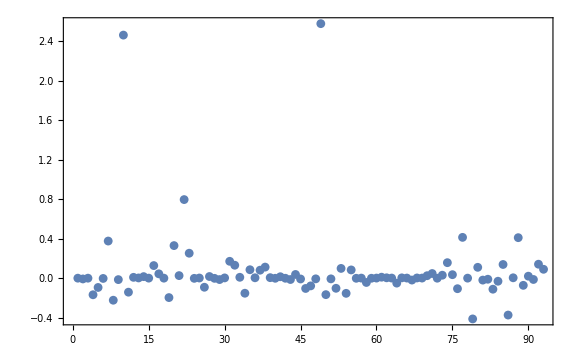
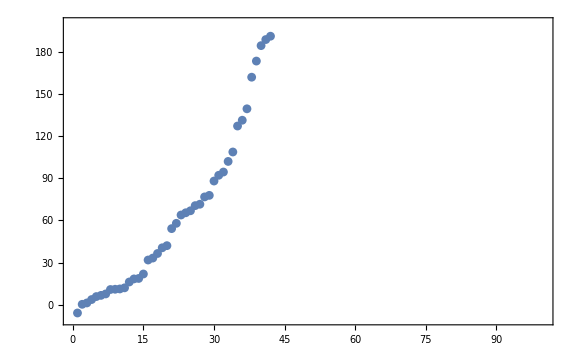
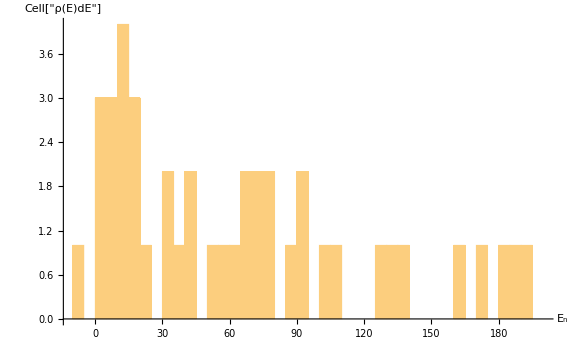
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
orderedEVSYHe3=Sort[Transpose[Eigensystem[tst=Transpose[He3Nmhi].He3Ham.He3Nmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&];
{ei,v0t}=orderedEVSYHe3[[1]];

dE=5;
Print["B(^3He) = ",ei];
Print["Dim_full^helion = ",Dimensions[He3Norm][[1]],"=^!",He3BasisDim,"   ;     Dim_(non - singular)^helion = ",Dimensions[v0t][[1]]]
Print["Lowest EV's:",orderedEVSYHe3[[1;;2,1]]]

fullv0=He3Nmhi.v0t;
Print["Norm=",fullv0.He3Norm.fullv0];
Grid[{{
ListPlot[Re[fullv0],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM basis vector}~n",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert {}^3\\text{He}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[orderedEVSYHe3[[All,1]],PlotRange->{{0,100},{-10,200}},Frame->True,FrameLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[orderedEVSYHe3[[All,1]],{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{"Cell[TextData[{\n\" \",\nCell[BoxData[FormBox[\nSubscriptBox[\"E\", \"n\"], TraditionalForm]]]\n}]]","Cell[\"ρ(E)dE\"]"}]
}}]
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the final state, i.e., J^π=(1/2)^- or J^π=(3/2)^- for the negative-parity rank-1 E_1 operator perturbing a helion;

```mathematica
matnames=FileNames["mat_*^-_BasNR-*"];
matnamesJ=Table[Select[matnames,StringMatchQ[#,"*"<>ToString[Subscript[I, n][[Inn]]]<>"*"]&],{Inn,Range[Length[Subscript[I, n]]]}];

LitNormHamMat=Table[readREAL8list[#]&/@Sort[matnamesJ[[Inn]],ToExpression[StringSplit[#1,"-"][[-1]]]<ToExpression[StringSplit[#2,"-"][[-1]]]&],{Inn,Range[Length[Subscript[I, n]]]}];

ActiveBasVFin=Table[Table[ReadList["Ssigbasv3heLIT_"<>ToString[Subscript[I, n][[Inn]]]<>"^-_BasNR-"<>ToString[nn]<>".dat"],{nn,Range[anzBas]}],{Inn,Range[Length[Subscript[I, n]]]}];

LITbasisDim=Table[IntegerPart[Sqrt[Length[#] 0.5]]&/@LitNormHamMat[[Inn]],{Inn,Range[Length[Subscript[I, n]]]}];

Print["N_(final - full) = ",LITbasisDim];
LitNorm=Table[ArrayReshape[LitNormHamMat[[Inn]][[#]][[1;;LITbasisDim[[Inn]][[#]]^2]],{LITbasisDim[[Inn]][[#]],LITbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
LitHam=Table[ArrayReshape[LitNormHamMat[[Inn]][[#]][[LITbasisDim[[Inn]][[#]]^2+1;;]],{LITbasisDim[[Inn]][[#]],LITbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];

Print["N_(final - active) = ",Length[#]&/@ActiveBasVFin];
Print["min/max Norm EV = ",Table[MinMax[Eigenvalues[LitNorm[[Inn]][[#]]]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}]];
```

N_(final - full) = {{68}}

N_(final - active) = {1}

min/max Norm EV = {{{0.0175809,5.42373}}}

#### The final state(s) (multi-pole perturbation on the helion’s ground state ^3 He ) -- in RGM Basis

=== I_n=1.5  BasNR: 1 ===

Final-state Basis dimension = {68,68}

min/max: {0.0175809,5.42373}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.596349,0.616067,0.674614,0.729317,0.829354}

===

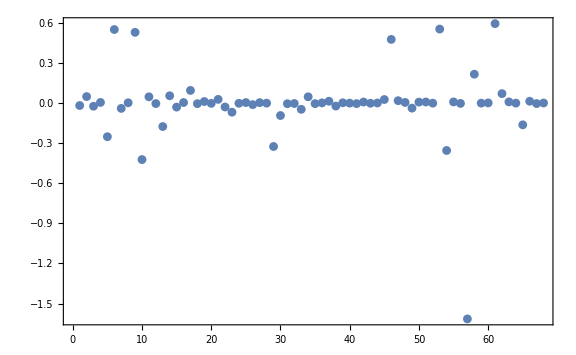
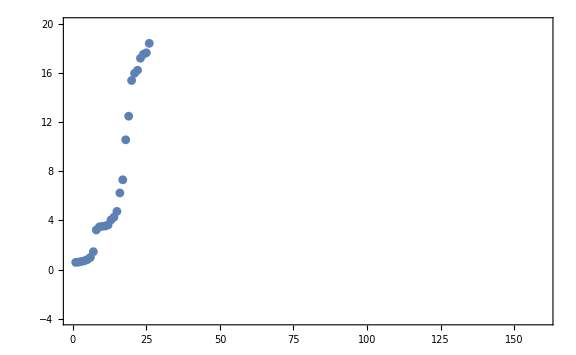
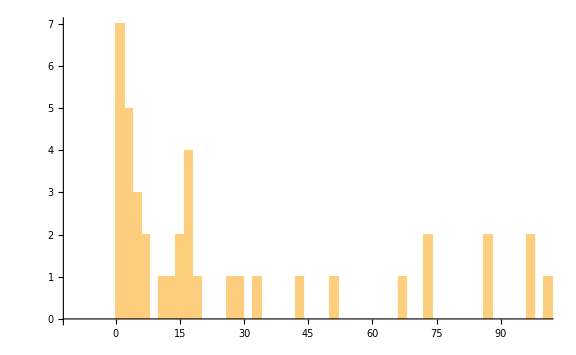

```mathematica
dE=2.;
plts={};
Do[
Do[
Print["=== I_n=",Subscript[I, n][[nj]],"  BasNR: ",nb," ==="];
Print["Final-state Basis dimension = ",Dimensions[LitNorm[[nj]][[nb]]]];
{LitNmh,LitNmhi}=matSqrts[LitNorm[[nj]][[nb]],thresholdLIT];
orderedEVSYLIT=Sort[Transpose[Eigensystem[tst=Transpose[LitNmhi].LitHam[[nj]][[nb]].LitNmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&];
{eth,v0t}=orderedEVSYLIT[[1]];

pltindex=50;
{eplt,v0plt}=orderedEVSYLIT[[pltindex]];
v0l=LitNmhi.v0plt;
Print["Norm=",v0l.LitNorm[[nj]][[nb]].v0l];
Print["lowest EV's: ",orderedEVSYLIT[[All,1]][[;;5]]];

plt1=ListPlot[Re[v0l],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM Basis-vector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert E_\\text{final}^{E_0+\\omega}\\right\\rangle",Magnification->2]},ImageSize->Large];

plt2=ListPlot[#[[1]]&/@orderedEVSYLIT,PlotRange->{{0,160},{-4,20}},Frame->True,FrameLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large];
plt3=Histogram[#[[1]]&/@orderedEVSYLIT,{dE},ImageSize->Large,PlotRange->{{-10,100},Automatic},AxesLabel->{MaTeX["E_n",Magnification->2],MaTeX["\\rho(E)dE",Magnification->2]}];
AppendTo[plts,{plt1,plt2,plt3}];
Print["==="];
,{nb,Range[anzBas]}];
,{nj,Range[1,Length[Subscript[I, n]]]}];
plts[[1]]
```

#### Read RHS ⟨ ϕ_(lit+D3)^n|O_Lm_L|ϕ_(lit+D3)^m ⟩, n,m∈{1,N_LIT/n_k+N_D3}

the calculation is parallel in n_k parts

Normalise coupling blocks!!!!

```mathematica
CouplingBlockjs={};
CouplingBlockjAs={};

Do[
If[Sign[Subscript[I, n][[nj]]]>=0,JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],2,"0"],JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],3,"0"]];

CouplingBlockj={};
CouplingBlockjA={};

Do[

CouplingBlock={};
CouplingBlockT={};
CouplingBlockTA={};

Do[
mM=Select[mLs,ClebschGordan[{multipolarity,#},{J0,mIn-#},{Subscript[I, n][[nj]],mIn}]≠0&];
	(*Why is mM unused here *)
fntmp = "InMIn_"<>ToString[Subscript[I, n][[nj]]]<>"_"<>ToString[mIn]<>"_BasNR-"<>ToString[nb]<>"."<>dt;
tmp =BinaryReadList[fntmp,datatype];

OutDim=Dimensions[tmp][[1]]/BareDims[[nb]][[1]];

test=ArrayReshape[tmp,{OutDim,BareDims[[nb]][[1]]}][[;;;;dH,;;;;dH]];
AppendTo[CouplingBlockT,{mIn,test}];
AppendTo[CouplingBlockTA,{mIn,test[[ActiveBasVFin[[nj]][[nb]],ActiveBasVHe3]]}];

,{mIn,mIns[[nj]]}];

AppendTo[CouplingBlockj,CouplingBlockT];
AppendTo[CouplingBlockjA,CouplingBlockTA];

,{nb,Range[anzBas]}];

AppendTo[CouplingBlockjs,CouplingBlockj];
AppendTo[CouplingBlockjAs,CouplingBlockjA];

,{nj,Range[1,Length[Subscript[I, n]]]}];

Print["Dim_active(⟨ψ|ο̂|helion⟩) = ",Table[Dimensions[CouplingBlockjAs[[Inn]][[#]][[1]][[2]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];

Print["Dim_bare(⟨ψ|ο̂|helion⟩)   = ",Table[Dimensions[CouplingBlockjs[[Inn]][[#]][[1]][[2]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];

Print["Dim(⟨ψ|Ĥ|ψ⟩) = ",Table[Dimensions[LitHam[[Inn]][[#]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
Print["Dim(⟨ψ|OverHat[1]|ψ⟩) = ",Table[Dimensions[LitNorm[[Inn]][[#]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
```

Dim_active(⟨ψ|ο̂|helion⟩) = {{{68,93}}}

Dim_bare(⟨ψ|ο̂|helion⟩)   = {{{68,93}}}

Dim(⟨ψ|Ĥ|ψ⟩) = {{{68,68}}}

Dim(⟨ψ|OverHat[1]|ψ⟩) = {{{68,68}}}

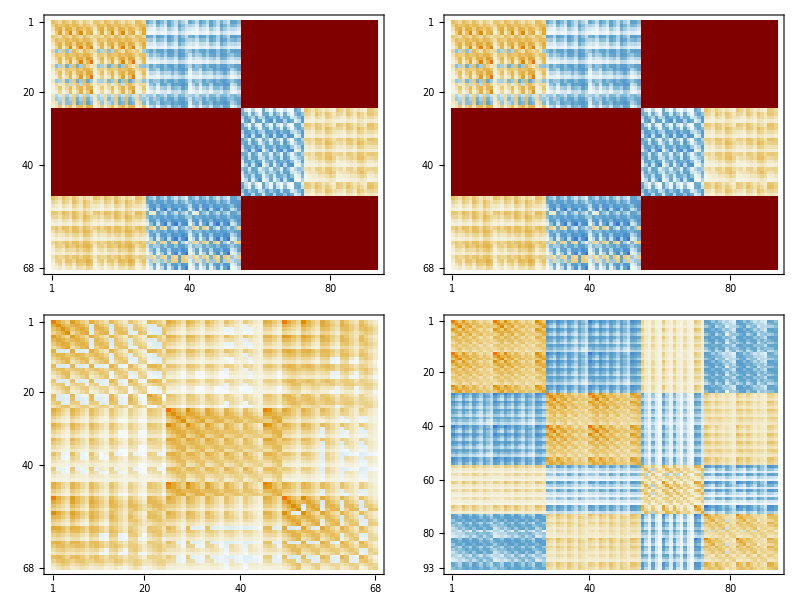

```mathematica
nb=1;nj=1;
Grid[{{
MatrixPlot[Chop[CouplingBlockjs[[nj]][[nb]][[1]][[2]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Coupling Matrix}",Magnification->2],ImageSize->Large]
,
MatrixPlot[Chop[CouplingBlockjAs[[nj]][[nb]][[1]][[2]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Optimal Coupling}",Magnification->2],ImageSize->Large]
},{
MatrixPlot[Chop[LitHam[[nj]][[nb]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Final-state Hamiltonian}",Magnification->2],ImageSize->Large]
,
MatrixPlot[Chop[He3Ham],FrameLabel->{MaTeX["{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Helion Hamiltonian}",Magnification->2],ImageSize->Large]
}}]
```

#### Analysis of RHS

```mathematica
OμRHSEB=normreg[thresholdLIT,He3Norm];
tmp=(Transpose[OμRHSEB].He3Ham).OμRHSEB; tmp=(tmp+Transpose[tmp])/2;
{λsHeEB,trfHeEB}=Eigensystem[tmp];
evgsEB=Flatten[trfHeEB[[TakeSmallest[λsHeEB->"Index",1]]]];
inhomoEB={};evgsEB=OμRHSEB.evgsEB;
Print["ev=",TakeSmallest[λsHeEB,1][[1]]," norm=",evgsEB.He3Norm.evgsEB];
```

ev=-5.77468 norm=1.

{68,93}{93}

{68,93}{93}

{68,93}{93}

«1 more identical outputs»

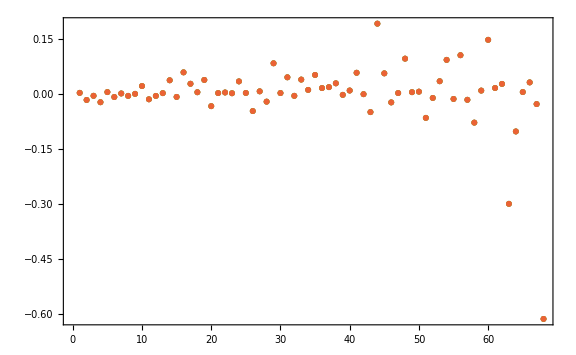

```mathematica
inhomoEB=Table[{},{nj,Length[Subscript[I, n]]}];
pltss={};
Do[
Do[
OμLHSEB=normreg[thresholdLIT,LitNorm[[nj]][[nb]]];
tmp=(Transpose[OμLHSEB].LitHam[[nj]][[nb]]).OμLHSEB;
tmp=(tmp+Transpose[tmp])/2;
{λfinalEB,trfLitEB}=Eigensystem[tmp];
Do[
tmp=CouplingBlockjAs[[nj]][[nb]][[mm]][[2]]/.Indeterminate->0;
Print[Dimensions[tmp],Dimensions[evgsEB]];
AppendTo[inhomoEB[[nj]],Transpose[OμLHSEB].(tmp.evgsEB)];
,{mm,Range[1,Length[mIns[[nj]]]]}
];AppendTo[pltss,ListPlot[inhomoEB[[nj]],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM Basis-vector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert O\\Big\\vert \\text{He}3 \\right\\rangle",Magnification->2]},ImageSize->Large]];
,{nb,Range[anzBas]}
];
,{nj,Range[1,Length[Subscript[I, n]]]}
];
Show[pltss]
```

#### “algebraic” LIT (norm zero-mode removal)

L_ν'L'νL^(I_f I_i;I_n)(k,k;σ)=(-)^(I_n-I_i+L-L'+ν')ρ(I_n,σ)∑_M_n ⟨ψ_(I_f I_i M_n)^ν'L'(k,σ)|ψ_(I_f I_i M_n)^νL(k,σ)⟩

#### Direct calculation of the (partial) strength functions

F_ν'L'νL^(I_f I_i)(k,k;E)=ρ(I_n,E) · ⟨I_f E_f||M^ν'L'(k')||I_n E ⟩⟨I_n E||M^(⋁L)(k)||I_i E_i ⟩
⇒ ρ(I_n,E)∝θ(E-E_i-k)

```mathematica
lpsisEV={};CumStrengthsEV={};

{μEV,transfEV}=Transpose[Select[Sort[Transpose[Eigensystem[He3Norm]],#1[[1]]<#2[[1]]&],#[[1]]>thresholdLIT&]];
OμRHSEV=(Transpose[transfEV].DiagonalMatrix[μEV^(-1/2)]);

{EvalsIEV,EvecsIEV}=Eigensystem[tmp=(Transpose[OμRHSEV].He3Ham).OμRHSEV;(tmp+Transpose[tmp])/2];
EvecGSiEV=OμRHSEV.Flatten[EvecsIEV[[TakeSmallest[EvalsIEV->"Index",1]]]];
EvalGSiEV=Min[EvalsIEV];
EvalGSiEV
{EvecGSiEV.He3Norm.EvecGSiEV,EvecGSiEV.He3Ham.EvecGSiEV}
```

-5.77468

{1.,-5.77468}

```mathematica
CumStrengthsJ={};pltsssJ={};
Do[
CumStrengths={};pltsss={};
Print[" J_final = ",Subscript[I, n][[nj]]];
Print["E_0^initial = ",EvalGSiEV,"    dim = ",Dimensions[EvalsIEV]];
Do[

{μlEV,transflEV}=Transpose[Select[Sort[Transpose[Eigensystem[LitNorm[[nj]][[nb]]]],#1[[1]]<#2[[1]]&],#[[1]]>thresholdLIT&]];
OμLHSEV=(Transpose[transflEV].DiagonalMatrix[μlEV^(-1/2)]);

{EvalsFEV,EvecsFEV}=Eigensystem[tmp=(Transpose[OμLHSEV].(LitHam[[nj]][[nb]])).OμLHSEV;(tmp+Transpose[tmp])/2];
{EvalsFEV,EvecsFEV}=Sort[{EvalsFEV,EvecsFEV},#1[[1]]<#2[[1]]&];
EvecGSfEV=OμLHSEV.Flatten[EvecsFEV[[TakeSmallest[EvalsFEV->"Index",1]]]];
EvalGSfEV=Min[EvalsFEV];

Print["Basisensemble ",nb,":  E_0^final  = ",EvalGSfEV,"    dim   = ",Dimensions[EvalsFEV]];
tmplEV=0;

Do[
inhomoEV=Transpose[OμLHSEV].((CouplingBlockjAs[[nj]][[nb]][[mm]][[2]]/.Indeterminate->0).EvecGSiEV);

tmplEV=tmplEV+(EvecsFEV.inhomoEV)^2;
,{mm,Length[mIns[[nj]]]}
];
lpsisEV=Transpose[{EvalsFEV,tmplEV}];

CumStrengthsEV=Transpose[{Sort[lpsisEV][[All,1]],Accumulate[Sort[lpsisEV][[All,2]]]}];

pl1=
ListPlot[lpsisEV,Joined->False,PlotMarkers->{{♔,12},{♗,12}},PlotRange->{{-3,7.5},{0,Automatic}},Filling->Axis,FillingStyle->{{Blue},{Red}},PlotRange->{Full,Full},AxesLabel->{MaTeX["\\text{E~[MeV]}",Magnification->2],MaTeX["\\left\\langle J^\\pi_{E_n=\\omega_\\text{lab}-E_0}\\Big\\vert\\widehat{E1}\\Big\\vert\\left({}^3\\text{He}\\right)_{E_0}^{1/2^+}\\right\\rangle^2",Magnification->2]},ImageSize->ImgSize];
pl2=
ListPlot[CumStrengthsEV,Joined->False,ImageSize->ImgSize,PlotRange->{{-3,350},{0,Automatic}},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["\\text{EV order}",Magnification->2]];

AppendTo[pltsss,{pl1,pl2}];
AppendTo[CumStrengths,CumStrengthsEV];

,{nb,Range[anzBas]}
];
AppendTo[pltsssJ,pltsss];
AppendTo[CumStrengthsJ,CumStrengths];
,{nj,Range[1,Length[Subscript[I, n]]]}
]
```

J_final = 1.5

E_0^initial = -5.77468    dim = {93}

Basisensemble 1:  E_0^final  = 0.596349    dim   = {68}

```mathematica
wce[wl_,MM_]:=wl (1+2 wl/MM)^(-1/2);
wla[wc_,MM_]:=wc (wc/MM+Sqrt[1+wc^2/MM^2]);
```

```mathematica
Integrate[8 Pi^2 x^2 (x Exp[-x^2/(4 α)-(ω-0.75 x^2)/α]/(3 Pi^1.5 α^2.5))^2/(2 √(ω-0.75 x^2)),{x,0,√(4. ω/3.)},Assumptions->{α∈Reals,α>0,ω∈Reals,ω>0}];

NielsF[ω_,α_]:=(ⅇ^(-(4 ω)/(3 α)) ((ω/α)^2 BesselI[0,(2 ω)/(3 α)]+((ω/α)^2-3 ω/α) BesselI[1,(2 ω)/(3 α)]))/(81 √3 α^2);
NielsC[λ_,α_]:=NIntegrate[NielsF[ω,α],{ω,0,λ}]

emin=-3;emax=150;
sc=0.975 (4 Pi/137)^-1;
αRGM=1.8;
```

```mathematica
CumStrengths[[1]]
```

{{0.596349,0.00192227},{0.616067,0.00192231},{0.674614,0.00229602},{0.729317,0.00291294},{0.829354,0.00291295},{1.00158,0.00953033},{1.46458,0.0120273},{3.22967,0.138843},{3.47202,0.142002},{3.52736,0.142103},{3.5514,0.143441},{3.63434,0.143532},{4.04923,0.146953},{4.26599,0.15504},{4.74107,0.155154},{6.23856,0.435474},{7.30943,0.627423},{10.5604,0.630323},{12.4775,0.631627},{15.3806,0.659704},{15.9634,0.969052},{16.2124,0.971586},{17.1897,1.02809},{17.5112,1.02862},{17.6308,1.16051},{18.3999,1.39888},{26.9479,1.85107},{29.0631,2.27118},{32.4125,2.2853},{42.2408,2.28572},{51.6438,2.28581},{66.2275,2.28766},{72.7733,2.28766},{72.9546,2.28776},{86.879,2.28985},{87.0001,2.29597},{96.4169,2.30807},{97.3527,2.3163},{100.395,2.31849},{102.299,2.37541},{105.271,2.37579},{107.821,2.4022},{111.068,2.41851},{118.067,2.43276},{139.425,2.43601},{159.402,2.43602},{177.094,2.4473},{178.511,2.44731},{217.894,2.44936},{282.689,2.45235},{314.01,2.45306},{434.763,2.45615},{490.124,2.45624},{809.002,2.45675},{850.05,2.45675},{982.899,2.45747},{1019.45,2.45747},{1050.29,2.45812},{1053.68,2.45812},{1067.4,2.45812},{1095.9,2.45812},{1156.8,2.45847},{1199.6,2.45847},{1281.8,2.45848},{1483.69,2.45848},{1693.85,2.45848},{2638.33,2.45851},{3236.57,2.45853}}

```mathematica
Min[CumStrengths[[1]][[All,1]]]
```

0.596349

1 cleaned sets out of 1

{2.45853}

Number 1

parametr values {a,b}

Number 2

parametr values {a,b,a2,b2,a3}

Number 3

parametr values {a,b,a2,b2,a3,b3,a4}

Number 1

{a→2.68972,b→0.000754638}

Residue=0.76004

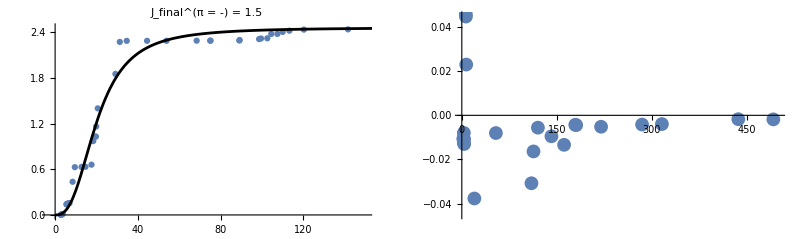

Number 2

{a→2.94032,b→0.000359498,a2→-0.0232449,b2→-0.0232162,a3→0.000139693}

Residue=0.654505

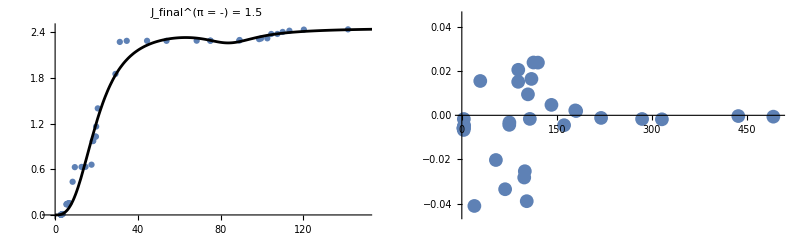

Number 3

{a→2.69093,b→0.000727184,a2→-0.04775,b2→-0.0478446,a3→0.000656735,b3→0.000657506,a4→-2.83031×10^-6}

Residue=0.548471

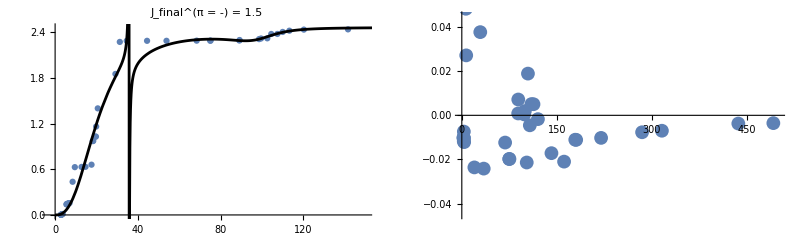

```mathematica
Block[{CumStrengthsJwithD={},
FittedThreshold={},
StrengthF={},StrengthF2={},
mn=0.,mn2=0.00,datasets=1,nFunc=3,
basIndices,a,b,c,a1,a2,a3,b2,c2,d2,b3,d,LowestEnergy, CutoffEnergy=-10,HighestEnergy=500},(*{1,2,3,4};*)
basIndices=Range[datasets];
listplots={};
Do[
(* exclude sets with first energy be below CutoffEnergy, i.e., spurious eigenvalues *)
cleanSet=Select[Sort[CumStrengthsJ[[nj]][[basIndices]]],#[[1,1]]>CutoffEnergy&];
Print[Length[cleanSet]," cleaned sets out of ",Length[CumStrengthsJ[[nj]][[basIndices]]]];Print[cleanSet[[All,-1,2]]];assymptote=Mean[cleanSet[[All,-1,2]]];
cleanSet=Flatten[cleanSet,1];
(*LowestEnergy=Min[cleanSet[[All,1]]];*)
LowestEnergy=-2.225;(*Deuteron binding energy*)
fitSetShifted={#[[1]]-LowestEnergy,#[[2]]}&/@cleanSet;
fitSetShifted=Select[fitSetShifted,#[[1]]<HighestEnergy&];
ffun[1]=(b(x+mn)^a)/(1+b/assymptote(x+mn)^a);par[1]={a,b};(*a,b,c*)
ffun[2]=(b(x+mn)^a)/(1+b/assymptote(x+mn)^a)(1+a2 (x+mn)+a3(x+mn)^2)/(1+b2 (x+mn)+a3(x+mn)^2);par[2]={a,b,a2,b2,a3};(*a,b2,b3,c,d*)
ffun[3]=(b(x+mn)^a)/(1+b/assymptote(x+mn)^a)(1+a2 (x+mn)+a3(x+mn)^2+a4(x+mn)^3)/(1+b2 (x+mn)+b3(x+mn)^2+a4(x+mn)^3);par[3]={a,b,a2, b2,a3,b3,a4};
par[4]=par[3];
start={2,0.05};
Do[Print[Style["Number "<>ToString[i],{Blue}]];
rr[i]=FindFit[fitSetShifted,ffun[i],Transpose[{par[i],start}],x,MaxIterations->5000];Print["parametr values ",par[i]];start=Join[par[i]/.rr[i],Table[0,Length[par[i+1]]-Length[par[i]]]],{i,nFunc}];
(*AppendTo[CumStrengthsJwithD,cleanSet];*)
FittedCum=Table[ffun[i]/.rr[i]/.x->e+LowestEnergy,{i,nFunc}];
dotplot=ListPlot[Table[{#[[1]]-LowestEnergy,#[[2]]}&/@CumStrengthsJ[[nj]][[basSet]],{basSet,datasets}],Joined->False,ImageSize->ImgSize,PlotRange->{{emin,emax},Full},AxesLabel->{MaTeX["E_\\text{final}~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},ImageSize->Large,PlotStyle->Directive[ColorData[12],PointSize[0.005]],PlotLabel->"J_final^(π = -) = "<>ToString[Subscript[I, n][[nj]]]];
Do[Print[Style["Number "<>ToString[i],{Large,Red}]];Print[rr[i]];Print[GraphicsRow[{Show[dotplot,Plot[{ffun[i]/.rr[i]},{x,0,HighestEnergy},PlotStyle->{Black},PlotRange->All]],ListPlot[tb=Table[{#[[1]]-LowestEnergy,#[[2]]-ffun[i]/.rr[i]/.x->#[[1]]-LowestEnergy}&/@CumStrengthsJ[[nj]][[basSet]],{basSet,datasets}];Print["Residue=",Plus@@Apply[Plus,tb[[;;,;;,2]]^2,{1}]];tb,Joined->False,ImageSize->ImgSize,PlotRange->{{0,HighestEnergy},{-0.045,0.045}}]}]],{i,nFunc}]
,{nj,Reverse[Range[Length[Subscript[I, n]]]]}];]
```

12 cleaned sets out of 12

{0.347752,0.347695,0.347627,0.347753,0.347743,0.347708,0.347696,0.347714,0.347637,0.347685,0.347751,0.34775}

assymptote=0.347709

Number 1

parameter values {b}

Number 2

parameter values {b,a2,b2,a3}

Number 3

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

parameter values {b,a2,b2,a3,b3,a4}

Number 1

{b→0.00341872}

Residue=0.770599

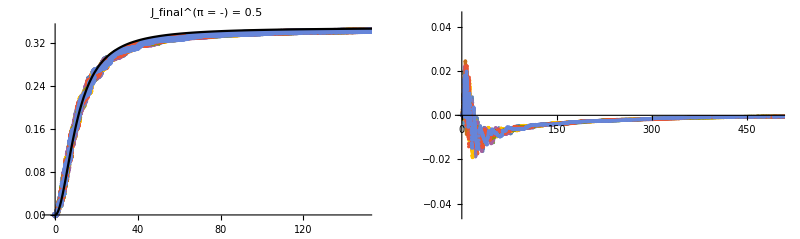

Number 2

{b→0.00433482,a2→-0.042613,b2→-0.0314992,a3→0.00654178}

Residue=0.165365

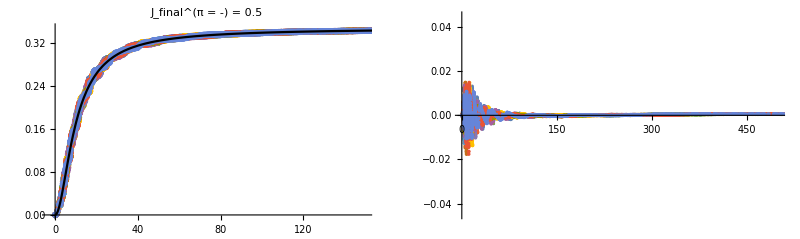

Number 3

{b→0.00433494,a2→-0.074302,b2→-0.0631836,a3→0.00789486,b3→0.00754253,a4→-0.000207384}

Residue=0.165352

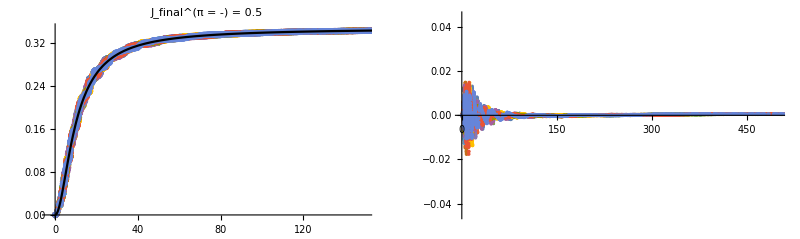

12 cleaned sets out of 12

{0.700816,0.701226,0.700796,0.700983,0.700737,0.70059,0.700587,0.700617,0.700715,0.700563,0.701341,0.700682}

assymptote=0.700804

Number 1

parameter values {b}

Number 2

parameter values {b,a2,b2,a3}

Number 3

parameter values {b,a2,b2,a3,b3,a4}

Number 1

{b→0.00710435}

Residue=3.15187

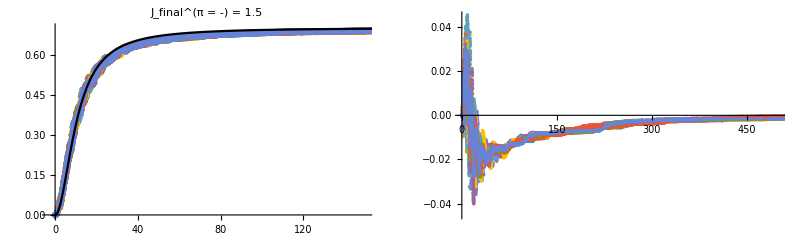

Number 2

{b→0.00881395,a2→-0.0125354,b2→0.00105797,a3→0.00769765}

Residue=0.611239

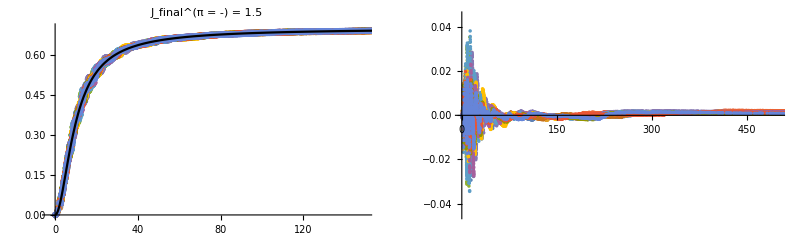

Number 3

{b→0.00890518,a2→-0.000270742,b2→0.0166144,a3→0.00897566,b3→0.00894337,a4→-0.0000147873}

Residue=5.63169

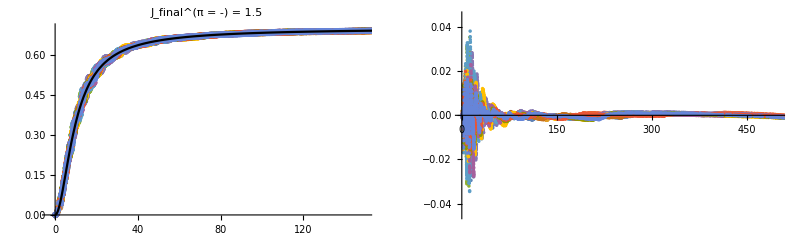

```mathematica
fits=Block[{CumStrengthsJwithD={},
FittedThreshold={},
StrengthF={},StrengthF2={},
mn=0.,mn2=0.00,datasets=12,nFunc=3,a=1.96,
basIndices,b,c,a1,a2,a3,a4,b2,c2,d2,b3,d,LowestEnergy, CutoffEnergy=-10,HighestEnergy=500,cleanSet,assymptote,fitSetShifted,ffun,par,start,rr,FittedCum,dotplot},(*{1,2,3,4};*)
basIndices=Range[datasets];
Table[
(* exclude sets with first energy be below CutoffEnergy, i.e., spurious eigenvalues *)
cleanSet=Select[Sort[CumStrengthsJ[[nj]][[basIndices]]],#[[1,1]]>CutoffEnergy&];
Print[Length[cleanSet]," cleaned sets out of ",Length[CumStrengthsJ[[nj]][[basIndices]]]];Print[cleanSet[[All,-1,2]]];assymptote=Mean[cleanSet[[All,-1,2]]];
Print["assymptote=",assymptote];
cleanSet=Flatten[cleanSet,1];
(*LowestEnergy=Min[cleanSet[[All,1]]];*)
LowestEnergy=-2.225;(*Deuteron binding energy*)
fitSetShifted={#[[1]]-LowestEnergy,#[[2]]}&/@cleanSet;
fitSetShifted=Select[fitSetShifted,#[[1]]<HighestEnergy&];
ffun[1]=(b(x+mn)^a)/(1+b/assymptote(x+mn)^a);par[1]={b};(*a,b,c*)
ffun[2]=(b(x+mn)^a)/(1+b/assymptote(x+mn)^a)(1+a2 (x+mn)+a3(x+mn)^2)/(1+b2 (x+mn)+a3(x+mn)^2);par[2]={b,a2,b2,a3};(*a,b2,b3,c,d*)
ffun[3]=(b(x+mn)^a)/(1+b/assymptote(x+mn)^a)(1+a2 (x+mn)+a3(x+mn)^2+a4(x+mn)^3)/(1+b2 (x+mn)+b3(x+mn)^2+a4(x+mn)^3);par[3]={b,a2, b2,a3,b3,a4};
par[4]=par[3];
start={0.05};
Do[Print[Style["Number "<>ToString[i],{Blue}]];
rr[i]=FindFit[fitSetShifted,ffun[i],Transpose[{par[i],start}],x,MaxIterations->5000];Print["parameter values ",par[i]];start=Join[par[i]/.rr[i],Table[0,Length[par[i+1]]-Length[par[i]]]],{i,nFunc}];
(*AppendTo[CumStrengthsJwithD,cleanSet];*)
FittedCum=Table[ffun[i]/.rr[i]/.x->e+LowestEnergy,{i,nFunc}];
dotplot=ListPlot[Table[{#[[1]]-LowestEnergy,#[[2]]}&/@CumStrengthsJ[[nj]][[basSet]],{basSet,datasets}],Joined->False,ImageSize->ImgSize,PlotRange->{{emin,emax},Full},AxesLabel->{MaTeX["E_\\text{final}~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},ImageSize->Large,PlotStyle->Directive[ColorData[12],PointSize[0.005]],PlotLabel->"J_final^(π = -) = "<>ToString[Subscript[I, n][[nj]]]];
Do[Print[Style["Number "<>ToString[i],{Large,Red}]];Print[rr[i]];Print[GraphicsRow[{Show[dotplot,Plot[{ffun[i]/.rr[i]},{x,0,HighestEnergy},PlotStyle->{Black},PlotRange->All]],ListPlot[tb=Table[{#[[1]]-LowestEnergy,#[[2]]-ffun[i]/.rr[i]/.x->#[[1]]-LowestEnergy}&/@CumStrengthsJ[[nj]][[basSet]],{basSet,datasets}];Print["Residue=",Plus@@Apply[Plus,tb[[;;,;;,2]]^2,{1}]];tb,Joined->False,ImageSize->ImgSize,PlotRange->{{0,HighestEnergy},{-0.045,0.045}}]}]],{i,nFunc}];FittedCum
,{nj,Range[Length[Subscript[I, n]]]}]];
```

```mathematica
Tsquared[Mf_,Mi_,λf_,θ_,strengthfunction_]:=
Module[{compo,ampli=0},
For[nJ=1,nJ≤Length[Subscript[I, n]],nJ++,
compo=strengthfunction[[nJ]];
For[Mm=-multipolarity,Mm≤multipolarity,Mm++,
For[Mmp=-multipolarity,Mmp≤multipolarity,Mmp++,
ampli+=compo]
]
];
Return[ampli]
]
```

```mathematica
fn[ind_]:=Block[{E0=0.001,Emax=150,dE=0.5,Eγ,Ji,Jf,Mi,Mf,labelj,EgammaShift=(-Bhe)/(ei),StrengthF2,E3=7.8,E2=2.2,E3mE2=5.6},
Ji=Jf=J0;Mi=Ji;Mf=Mi;
labelj=("J = "<>ToString[#])&/@Subscript[I, n];
StrengthF2=D[fits[[;;,ind]],e];
strengthfunction=StrengthF2/.e->(Eγ-E3+2E2);
fudgi=1.0;
kinfac=((fudgi*( (2Pi)^2 )*αfine )*(Eγ-E3+2E2));

lf=1;
plotCrossSec=Show[Plot[Re[kinfac(*(strengthfunction[[1]]+strengthfunction[[2]])(2multipolarity+1)^2*)(strengthfunction[[1]] 4+strengthfunction[[2]]16)]
,{Eγ,E3mE2,Emax},PlotRange->Full,LabelStyle->Directive[Larger],AxesLabel->{"E_γ [MeV]","SuperscriptBox[(2  π),2] [fm^-2] ·("<>ToString[Style[fudgi,Red],TraditionalForm]<>")"}(*,Filling->cycl*),ImageSize->ImgSize,PlotStyle->{Thick,Dashed},PlotLegends->{"LIT"}],ListPlot[He3DataFm2,PlotLegends->"σ_tot data"],PlotRange->{{0,140},{0.,2.2}},AxesOrigin->{0.,0.}
]
]
```

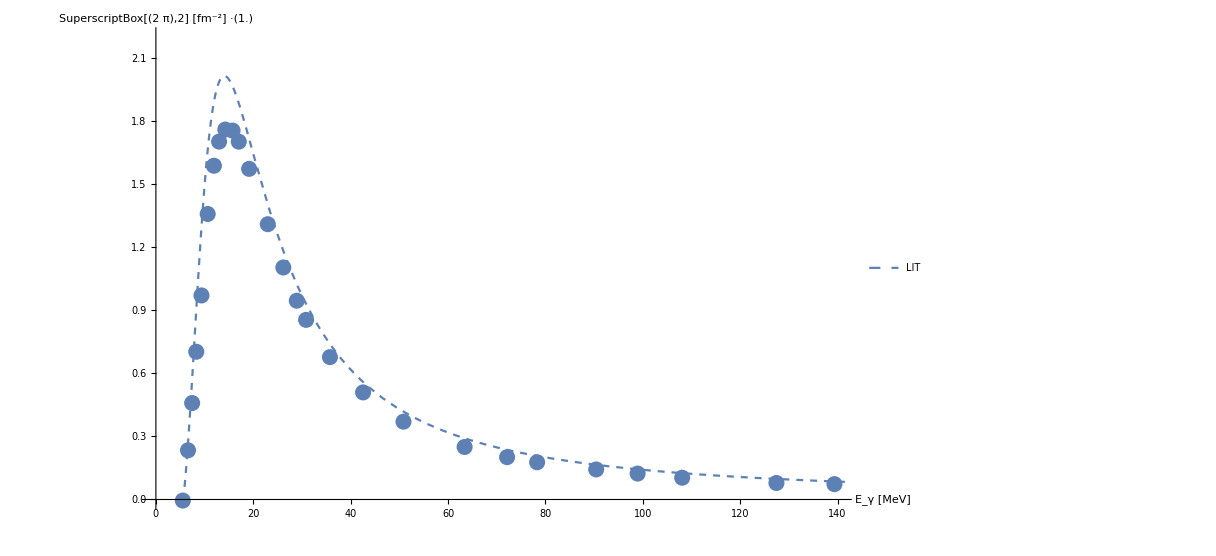

```mathematica
fn[2]
```

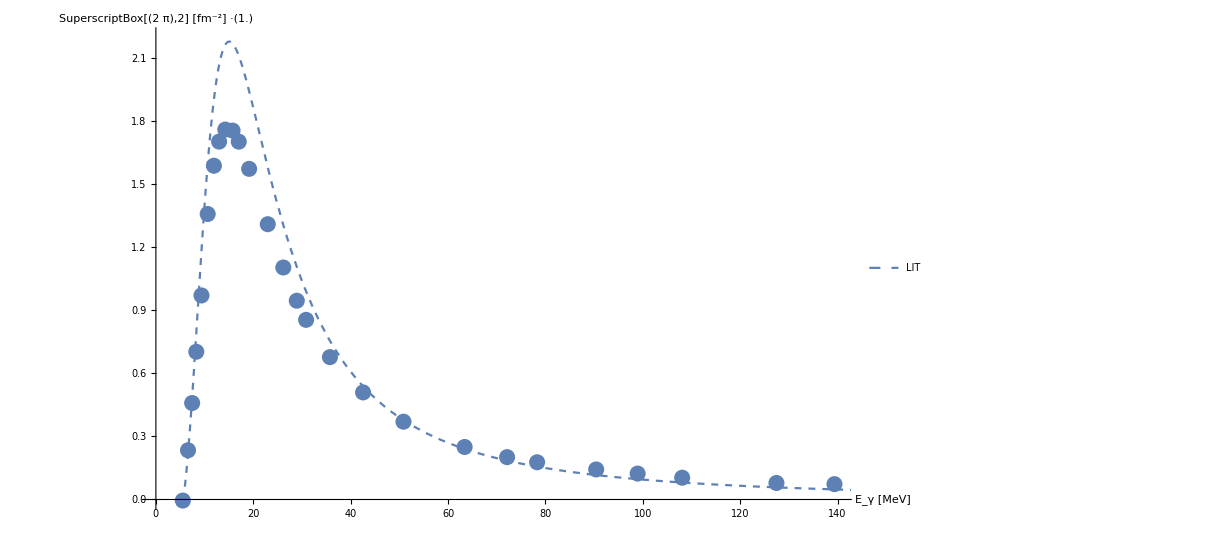

```mathematica
fn[1]
```

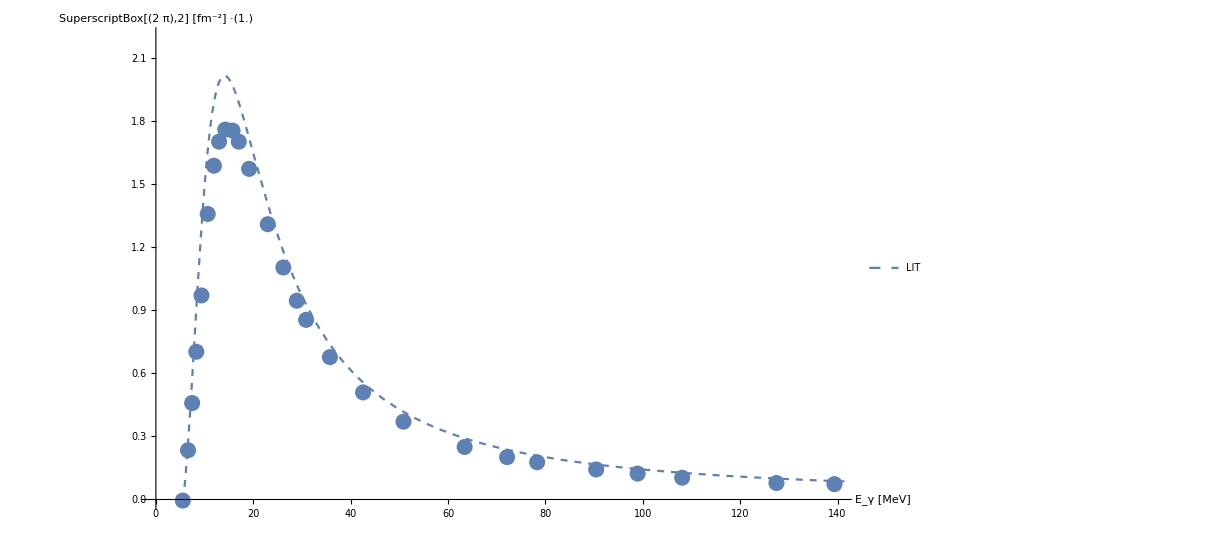

```mathematica
fn[3]
```

WolframAlphaQueryParseResults

mb

```mathematica
UnitConvert[ Quantity[1.,"fm"]^-2/(Quantity[1,"PlanckConstant"]/(2π)Quantity[1,"SpeedOfLight"])^-1/Quantity[1,"millibarn"]]
```

3.16153×10^35 kg/(m s^2)

```mathematica
UnitConvert[ Quantity[1.,"MeV"]^-1Quantity[1,"fm"]/(Quantity[1,"PlanckConstant"]/(2π)Quantity[1,"SpeedOfLight"])^-1/Quantity[1,"millibarn"]]
```

1973.27

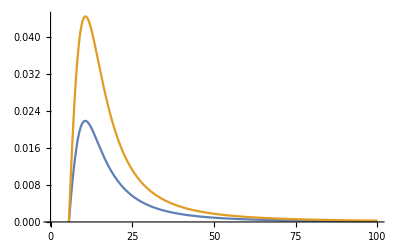

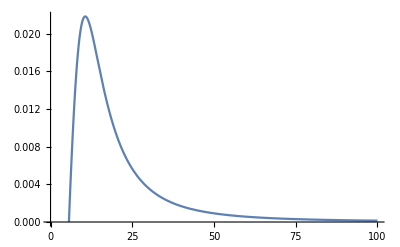

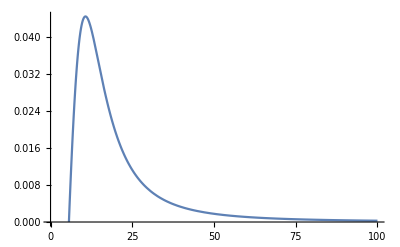

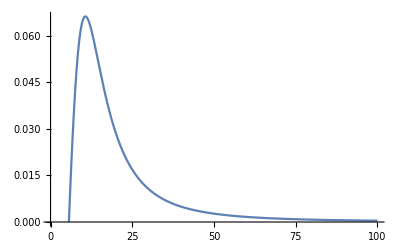

```mathematica
E3=7.8;E2=2.2;E3mE2=5.6;
StrengthF2=D[fits[[;;,2]],e];
strengthfunction=StrengthF2/.e->(e-E3+2E2);
Plot[strengthfunction,{e,0,100},PlotRange->Full]
Plot[strengthfunction[[1]],{e,0,100},PlotRange->Full]
Plot[strengthfunction[[2]],{e,0,100},PlotRange->Full]
Plot[(strengthfunction[[1]]+strengthfunction[[2]]),{e,0,100},PlotRange->Full]
```

```mathematica
fn2[ind_]:=Block[{E0=0.001,Emax=150,dE=0.5,Eγ,Ji,Jf,Mi,Mf,labelj,EgammaShift=(-Bhe)/(ei),StrengthF2,E3=7.8,E2=2.2,E3mE2=5.6},
Ji=Jf=J0;Mi=Ji;Mf=Mi;
labelj=("J = "<>ToString[#])&/@Subscript[I, n];
StrengthF2=D[fits[[;;,ind]],e];
strengthfunction=StrengthF2/.e->(Eγ-E3+2E2);
fudgi=1.0;
iif=1/2;
kinfac=(fudgi*(4π)/(√2.)1/(√3.)*6 π^2);

lf=1;
plotCrossSec=Show[Plot[((SixJSymbol[{1,1,0},{1/2,1/2,1/2}]*strengthfunction[[1]]-SixJSymbol[{1,1,0},{1/2,1/2,3/2}]*strengthfunction[[2]])*(4π)/(√2.)*1/(√3.)*6 π^2*Eγ*1/(16π))
,{Eγ,E3mE2,Emax},PlotRange->Full,LabelStyle->Directive[Larger],AxesLabel->{"E_γ [MeV]","SuperscriptBox[(2  π),2] [fm^-2] ·("<>ToString[Style[fudgi,Red],TraditionalForm]<>")"}(*,Filling->cycl*),ImageSize->ImgSize,PlotStyle->{Thick,Dashed},PlotLegends->{"LIT"}],ListPlot[He3DataFm2,PlotLegends->"σ_tot data"],PlotRange->All,AxesOrigin->{0.,0.}
]
]
```

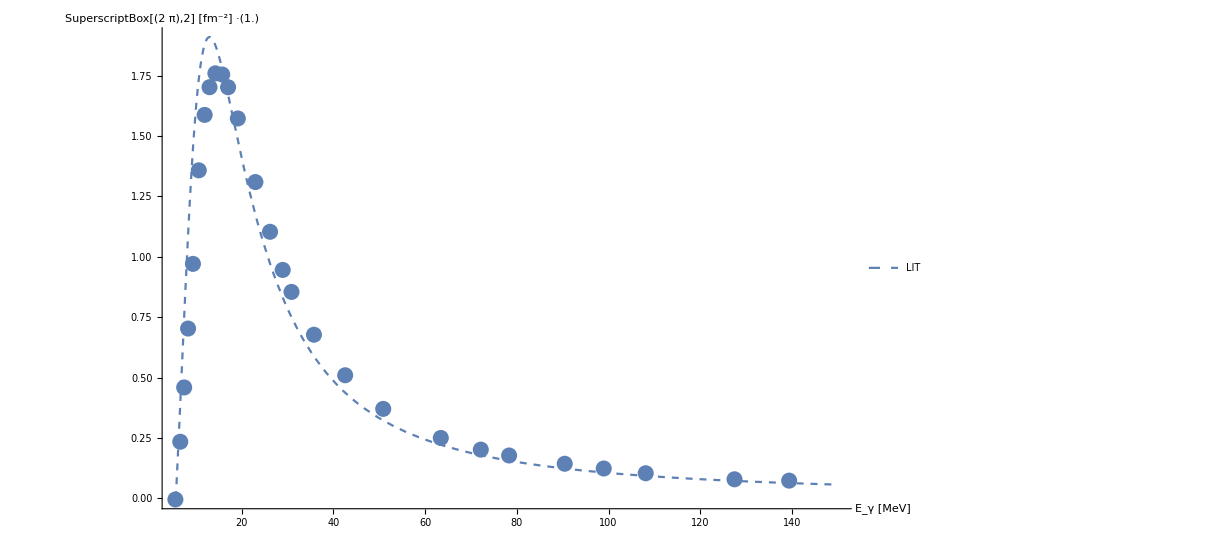

```mathematica
fn2[2]
```

```mathematica
1/50.
```

0.02

```mathematica
1/hbarc
```

0.00506769

```mathematica
fn3[ind_]:=Block[{E0=0.001,Emax=150,dE=0.5,Eγ,Ji,Jf,Mi,Mf,labelj,EgammaShift=(-Bhe)/(ei),StrengthF2,E3=7.8,E2=2.2,E3mE2=5.6},
Ji=Jf=J0;Mi=Ji;Mf=Mi;
labelj=("J = "<>ToString[#])&/@Subscript[I, n];
StrengthF2=D[fits[[;;,ind]],e];
strengthfunction=StrengthF2/.e->(Eγ-E3+2E2);
ii=1/2;
facr=((4π)/(√((2*ii)+1))*1/(√3.));

lf=1;
plotCrossSec=Show[Plot[((1/(√6)*strengthfunction[[1]]-1/(√6)strengthfunction[[2]])*facr*-6 π^2*Eγ)
,{Eγ,E3mE2,Emax},PlotRange->Full,LabelStyle->Directive[Larger],AxesLabel->{"E_γ [MeV]","SuperscriptBox[(2  π),2] [fm^-2] ·("<>ToString[Style[fudgi,Red],TraditionalForm]<>")"}(*,Filling->cycl*),ImageSize->ImgSize,PlotStyle->{Thick,Dashed},PlotLegends->{"LIT"}],ListPlot[He3DataFm2,PlotLegends->"σ_tot data"],PlotRange->All,AxesOrigin->{0.,0.}
]
]
```

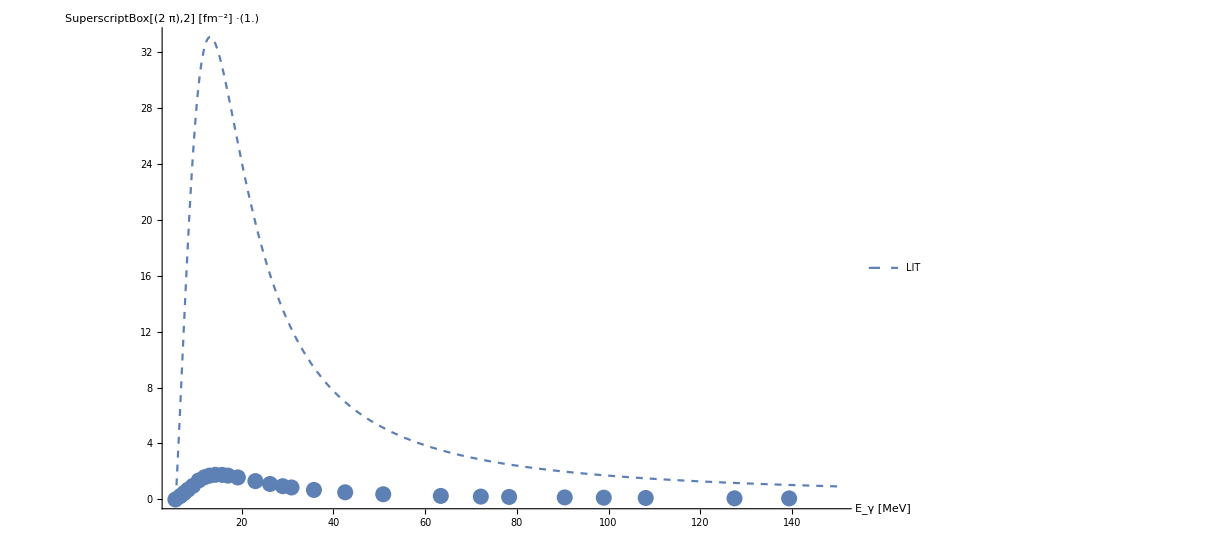

```mathematica
fn3[2]
```

#### σ_tot=(2π)^2 α·E_γ ∑_(J,M) JM OverHat[E1](J_0 m_0)^2

```mathematica
SixJSymbol[{1,1,0},{1/2,1/2,1/2}]
```

1/(√6)

```mathematica
SixJSymbol[{1,1,0},{1/2,1/2,3/2}]
```

-1/(√6)

```mathematica
SixJSymbol[{1,1,0},{1/2,1/2,1/2}]
```

1/(√6)

```mathematica
SixJSymbol[{1,1,0},{1/2,1/2,3/2}]
```

-1/(√6)

```mathematica
SixJSymbol[{1,1,0},{1,1,1/2}]










































Block[{CumStrengthsJwithD={},
FittedThreshold={},
StrengthF={},StrengthF2={},
mn=0.,mn2=0.00,datasets=12,
basIndices,a,b,c,a1,a2,a3,b2,c2,d2,b3,d,LowestEnergy, CutoffEnergy=-10,HighestEnergy=300},(*{1,2,3,4};*)
basIndices=Range[datasets];
listplots={};
Do[
(* exclude sets with first energy be below CutoffEnergy, i.e., spurious eigenvalues *)
cleanSet=Select[Sort[CumStrengthsJ[[nj]][[basIndices]]],#[[1,1]]>CutoffEnergy&];
Print[Length[cleanSet]," cleaned sets out of ",Length[CumStrengthsJ[[nj]][[basIndices]]]];Print[cleanSet[[All,-1,2]]];assymptote=Mean[cleanSet[[All,-1,2]]];
cleanSet=Flatten[cleanSet,1];
(*LowestEnergy=Min[cleanSet[[All,1]]];*)
LowestEnergy=-2.225;(*Deuteron binding energy*)
fitSetShifted={#[[1]]-LowestEnergy,#[[2]]}&/@cleanSet;
fitSetShifted=Select[fitSetShifted,#[[1]]<HighestEnergy&];
ffun[1]=(b(x+mn)^a)/(1+b/assymptote(x+mn)^a);par[1]={a,b};(*a,b,c*)
ffun[2]=(b2(x+mn)^a)/(1+d2(x+mn)^(a/2.)+b2/assymptote(x+mn)^a);par[2]={a,b2,d2};(*a2,b2,c2,d2*)
ffun[3]=(b(x+mn)^a)/(1+b/assymptote(x+mn)^a)(1+a2 (x+mn)+a3(x+mn)^2)/(1+b2 (x+mn)+a3(x+mn)^2);par[3]={a,b,a2,a3,b2};(*a,b2,b3,c,d*)
ffun[4]=(b(x+mn)^a)/(1+b/assymptote(x+mn)^a)(1+a2 (x+mn)+a3(x+mn)^2+a4(x+mn)^3)/(1+b2 (x+mn)+b3(x+mn)^2+a4(x+mn)^3);par[4]={a,b,a2,a3,a4, b2,b3};
ffun[5]=(b(x+mn)^a)/(1+b/assymptote(x+mn)^a)(1+a2 (x+mn)^0.5+a3(x+mn)^1.5+a4(x+mn)^2.5)/(1+b2 (x+mn)^0.5+b3(x+mn)^1.5+a4(x+mn)^2.5);par[5]={a,b,a2,a3,a4, b2,b3};
ffun[6]=(b(x+mn)^a)/(1+b/assymptote(x+mn)^a)(1+a2 (x+mn)+a3(x+mn)^1.5+a4(x+mn)^2.5)/(1+b2 (x+mn)+b3(x+mn)^1.5+a4(x+mn)^2.5);par[6]={a,b,a2,a3,a4, b2,b3};
ffun[7]=(b(x+mn)^a)/(1+b/assymptote(x+mn)^a)(1+a2 (x+mn)^1.5+a3(x+mn)^2.5+a4(x+mn)^3.5)/(1+b2 (x+mn)^1.5+b3(x+mn)^2.5+a4(x+mn)^3.5);par[7]={a,b,a2,a3,a4, b2,b3};
Do[Print[Style["Number "<>ToString[i],{Blue}]];
rr[i]=FindFit[fitSetShifted,ffun[i],Evaluate[par[i]],x,MaxIterations->5000];Print[par[i]],{i,7}];
(*AppendTo[CumStrengthsJwithD,cleanSet];*)
FittedCum=Table[ffun[i]/.rr[i]/.x->e+LowestEnergy,{i,7}];
dotplot=ListPlot[Table[{#[[1]]-LowestEnergy,#[[2]]}&/@CumStrengthsJ[[nj]][[basSet]],{basSet,datasets}],Joined->False,ImageSize->ImgSize,PlotRange->{{emin,emax},Full},AxesLabel->{MaTeX["E_\\text{final}~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},ImageSize->Large,PlotStyle->Directive[ColorData[12],PointSize[0.005]],PlotLabel->"J_final^(π = -) = "<>ToString[Subscript[I, n][[nj]]]];
Do[Print[Style["Number "<>ToString[i],{Large,Red}]];Print[rr[i]];Print[GraphicsRow[{Show[dotplot,Plot[{ffun[i]/.rr[i]},{x,0,HighestEnergy},PlotStyle->{Black},PlotRange->All]],ListPlot[tb=Table[{#[[1]]-LowestEnergy,#[[2]]-ffun[i]/.rr[i]/.x->#[[1]]-LowestEnergy}&/@CumStrengthsJ[[nj]][[basSet]],{basSet,datasets}];Print["Residue=",Plus@@Apply[Plus,tb[[;;,;;,2]]^2,{1}]];tb,Joined->False,ImageSize->ImgSize,PlotRange->{{0,HighestEnergy},{-0.045,0.045}}]}]],{i,7}]
,{nj,Reverse[Range[Length[Subscript[I, n]]]]}];]
```

SixJSymbol::tri: SixJSymbol[{1,1,0},{1,1,1/2}] is not triangular.

0

12 cleaned sets out of 12

{0.700816,0.701226,0.700796,0.700983,0.700737,0.70059,0.700587,0.700617,0.700715,0.700563,0.701341,0.700682}

Number 1

{a,b}

Number 2

{a,b2,d2}

Number 3

{a,b,a2,a3,b2}

Number 4

$Aborted